```mathematica
g=9.8; (*grav. constant*)

x0=0;
y0 = 0; 
v= 30;
vt =100;(*starting from rest*)
(*ϕ=y;
t=x;*)
th = 50 Pi/180; f==15
ode1 = x''[t]==(-g  x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2];
ode2 = y''[t] == -g(1 + (y'[t]/vt^2)Sqrt[x'[t]^2 + y'[t]^2]);
```

f==15

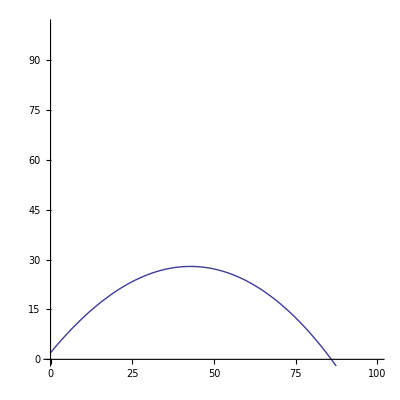

show[-Graphics-]

```mathematica
sol =NDSolve[{ode1, ode2, x[0]==0,x'[0] == v Cos[th],y[0] == 2, y'[0] == v Sin[th]},  {x,y}, {t,0,200}];
myplot1 = ParametricPlot[Evaluate[{x[t], y[t]}/.sol], {t, 0, 200}, PlotRange-> {{0, 100}, {0,100}}]
show[myplot1]
```

```mathematica
ode3 = x1[t] == x0 + v Cos[th t]; ode4 = y1 == y0 + v Sin[th t] - .5 g (t^2);
 x1[0]==0;x1'[0] == v Cos[th];y1[0] == 2; y1'[0] == v Sin[th];
sol2 =Solve[{ode3, ode4},  {x1,y1}, {t,0,200}];
myplot2 = ParametricPlot[Evaluate[{ode3, ode4}/.sol2], {t, 0, 200}, PlotRange-> {{0, 100}, {0,100}}]
```

Solve::ivar: 0 is not a valid variable.

ReplaceAll::reps: {Solve[{x1[t] == 30\ Cos[5\ π\ t/18], y1 == -4.9\ t^2 + 30\ Sin[Times[« 3 »]]}, {x1, y1}, {t, 0, 200}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ivar: 0.00408163 is not a valid variable.

ReplaceAll::reps: {Solve[{x1[0.00408163] == 29.9998, y1 == 0.106775}, {x1, y1}, {0.00408163, 0, 200}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ivar: 0.00408163 is not a valid variable.

ReplaceAll::reps: {Solve[{x1[0.00408163] == 29.9998, y1 == 0.106775}, {x1, y1}, {0.00408163, 0., 200.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Solve::ivar: 4.08571 is not a valid variable.

General::stop: Further output of Solve :: ivar will be suppressed during this calculation.

-Graphics-

```mathematica
ode1 = x''[t]==(-g  x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2];
ode2 = y''[t] == -g(1 + (y'[t]/vt^2)Sqrt[x'[t]^2 + y'[t]^2]);
```

```mathematica
Manipulate[
g=9.8; x1[t] == x0 + v Cos[th t]; y1 == y0 + v Sin[th t] - .5 g (t^2);
Module[
{sol= NDSolve[{x''[t]==(-g  x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1 + (y'[t]/vt^2)Sqrt[x'[t]^2 + y'[t]^2]), x[0]==0,x'[0] == v Cos[th],y[0] == 2, y'[0] == v Sin[th]},  {x,y}, {t,0,200}]},
ParametricPlot[{Evaluate[{x[t], y[t]}/.sol]},{t, 0, 200},PlotStyle-> {{Blue},{Red}},PlotRange-> {{0, 100}, {0,50}},AxesLabel->{"Distance","Altitude"}, ImageSize->{500,300} ]],
{{v,30,"initial velocity(m/s)"},0,100,Appearance->"Labeled"}
, {{vt, 1, "Terminal Velocity(m/s)"}, 1, 100, Appearance -> "Labeled"}, {{th,50*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"}(*,{{t, 1, "Time(s)"},0, 10, Appearance->"Labeled"}*)]
```

```mathematica
myplot1 = Plot[(180/Pi) θ[t]/.sol,{t,0,20},PlotStyle-> RGBColor[0,0,1],PlotRange-> All];
omega=√(g/l);
```

```mathematica
approx = (180/Pi) θ0 Cos[omega*t];
myplot2=Plot[approx,{t,0,20},PlotStyle-> RGBColor[1,0,0],PlotRange-> All];
```

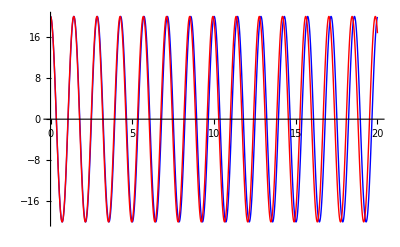

```mathematica
Show[{myplot1,myplot2}]
```

```mathematica
Manipulate[
g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```